```mathematica
<<Units`
```

```mathematica
<<PhysicalConstants`
```

General::obspkg: PhysicalConstants` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

#### Trigger, WD mass

```mathematica
trigger[ρ_]:=Piecewise[{{10^-5*(ρ/(5*10^9))^(-1/2),ρ>10^8},{1/(10000 √2)*(ρ/10^8)^-2,ρ<=10^8}}]
```

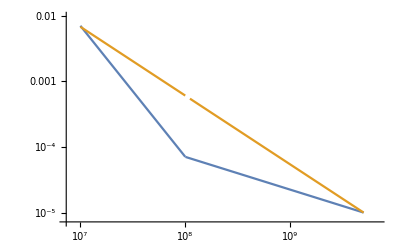

```mathematica
LogLogPlot[{trigger[ρ],10^-5*(ρ/(5*10^9))^-1.05},{ρ,5*10^9,10^7}]
```

```mathematica
logLogRegionPlot[rplot_]:=Module[{pts,pgon},pts=Cases[Normal@rplot,Line[a__]:>a,Infinity];
pgon={EdgeForm[],Directive[RGBColor[0.368417,0.506779,0.709798],AbsoluteThickness[1.6],Opacity[0.3]],Cases[Normal@rplot,Polygon[_],Infinity]};
ListLogLogPlot[pts,Joined->True,Frame->True,PlotRange->All,AspectRatio->1,Axes->False,PlotStyle->ColorData[1][1],Epilog->(pgon/.{x_,y_?NumericQ}:>Log@{x,y})]]
```

```mathematica
fSpace[min_,max_,steps_,f_: Log]:=InverseFunction[f]/@Range[f@min,f@max,(f@max-f@min)/(steps-1)]
```

```mathematica
WD=Import["/Users/NewUser/Documents/Berkeley/Second Year/Q balls/WD.csv"];
```

```mathematica
WDrad=Import["/Users/NewUser/Documents/Berkeley/Second Year/Q balls/WDradius.csv"];
```

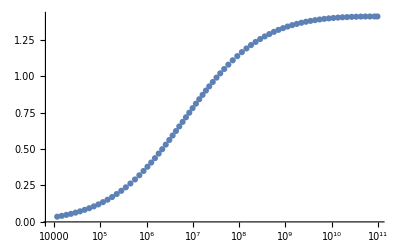

```mathematica
ListLogLinearPlot[WD]
```

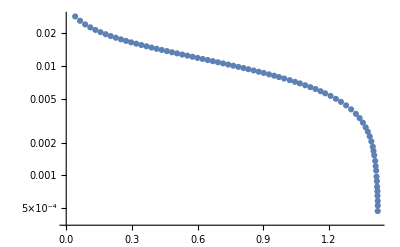

```mathematica
ListLogPlot[WDrad]
```

```mathematica
WDplot=Interpolation[WD]
```

10
InterpolatingFunction[{{11675.9, 9.77451 10  }}, <>]

```mathematica
Radplot=Interpolation[WDrad]
```

InterpolatingFunction[{{0.0407984, 1.42331}}, <>]

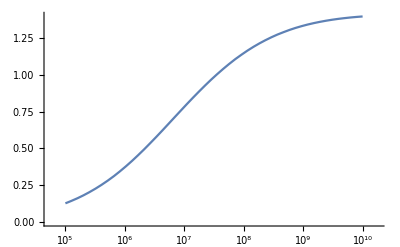

```mathematica
LogLinearPlot[WDplot[x],{x,10^5,10^10}]
```

#### Escape velocity (4*10^-3-10^-2 range in radius for white dwarf)

```mathematica
(7*10^5 Kilo Meter)*4*10^-3
```

2800 Kilo Meter

```mathematica
SolarRadius
```

6.9599×10^8 Meter

```mathematica
vesc[M_]:=Convert[Sqrt[2GravitationalConstant*M/Radplot[M]*SolarMass/SolarRadius] 1/SpeedOfLight,d]
```

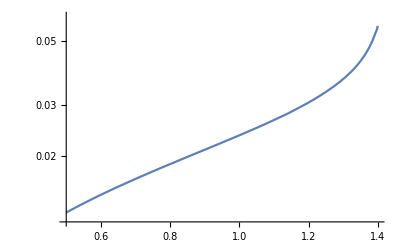

```mathematica
LogPlot[vesc[M],{M,0.5,1.4}]
```

```mathematica
Convert[1 Centimeter/SpeedOfLight,Second]//N
```

3.33564×10^-11 Second

#### transit time Δt of Q ball as function of density

InterpolatingFunction::dmval: Input value {1.13018745×10^434370} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dprec: The precision of input value {1.13018745×10^434370} and/or the interpolation grid is insufficient to compute the value.

InterpolatingFunction::dmval: Input value {1.13018745×10^434370} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dprec: The precision of input value {1.13018745×10^434370} and/or the interpolation grid is insufficient to compute the value.

InterpolatingFunction::dmval: Input value {3.98546273×10^516831} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dprec: The precision of input value {3.98546273×10^516831} and/or the interpolation grid is insufficient to compute the value.

General::stop: Further output of InterpolatingFunction::dprec will be suppressed during this calculation.

LogLogPlot::exclul: {Im[(InterpolatingFunction[{{11675.9,9.77451×10^10}},«3»,{Automatic}][ⅇ^ρ])/(«1»)]-0,(100000000-ⅇ^ρ)-0,(-100000000+ⅇ^ρ)-0,Im[ⅇ^ρ]-0} must be a list of equalities or real-valued functions.

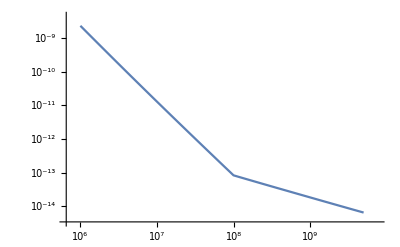

```mathematica
LogLogPlot[trigger[ρ]/vesc[WDplot[ρ]]*3.33564095198152*^-11,{ρ,10^6,5*10^9}]
```

#### τdiff for trigger size defined to scale as 1/ρ. Sufficiently slow diffusion time condition:

InterpolatingFunction::dmval: Input value {1.13018745×10^434370} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dprec: The precision of input value {1.13018745×10^434370} and/or the interpolation grid is insufficient to compute the value.

InterpolatingFunction::dmval: Input value {1.13018745×10^434370} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dprec: The precision of input value {1.13018745×10^434370} and/or the interpolation grid is insufficient to compute the value.

InterpolatingFunction::dmval: Input value {3.98546273×10^516831} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dprec: The precision of input value {3.98546273×10^516831} and/or the interpolation grid is insufficient to compute the value.

General::stop: Further output of InterpolatingFunction::dprec will be suppressed during this calculation.

LogLogPlot::exclul: {Im[(InterpolatingFunction[{{11675.9,9.77451×10^10}},«3»,{Automatic}][ⅇ^ρ])/(InterpolatingFunction[{{«2»}},«3»,{Automatic}][InterpolatingFunction[{«1»},«3»,{«1»}][«1»]])]-0,«1»,«1»,Im[ⅇ^ρ]-0} must be a list of equalities or real-valued functions.

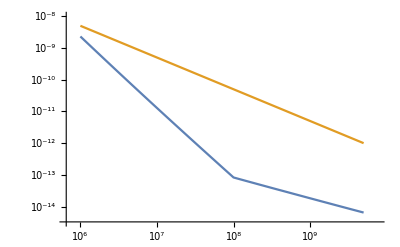

```mathematica
LogLogPlot[{trigger[ρ]/vesc[WDplot[ρ]]*3.33564095198152*^-11,10^-12((5*10^9)/ρ)},{ρ,10^6,5*10^9}]
```

#### Constraints

```mathematica
Radplot[1.25]SolarRadius
```

3.32847×10^6 Meter

```mathematica
vesc[1.25]
```

0.0333087

```mathematica
Convert[ρ (Giga*ElectronVolt)/Centimeter^3*(Giga Year)*Pi*(Radplot[M]SolarRadius)^2*(vesc[M])^2/(10^-3)1/SpeedOfLight,Gram]/.{ρ->10^3,M->1.25}
```

6.50805×10^23 Gram

#### Trigger size + Explosiveness

```mathematica
triggermass=Table[{WDplot[ρ],trigger[ρ]},{ρ,fSpace[10^6,5*10^9,1000]}];
```

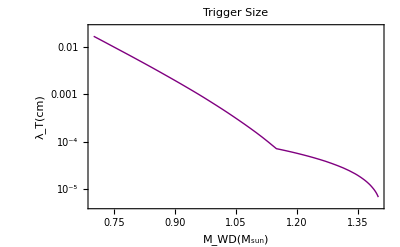

```mathematica
LogPlot[Interpolation[triggermass][M],{M,0.7,1.4},PlotLabel->"Trigger Size",Frame->True,PlotStyle->{Thick,Purple},FrameLabel->{"M_WD(M_sun)","λ_T(cm)"},FrameStyle->Black]
```

```mathematica
{Interpolation[triggermass][0.7],Interpolation[triggermass][1.2],Interpolation[triggermass][1.3]}//N
```

{0.0170754,0.0000564303,0.000030864}

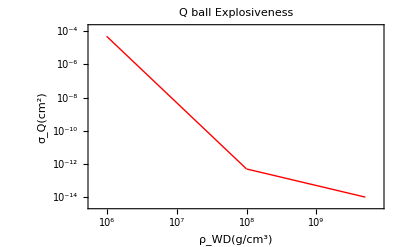

```mathematica
LogLogPlot[10^-4*trigger[ρ]^2,{ρ,10^6,5*10^9},FrameLabel->{"ρ_WD(g/cm^3)","σ_Q(cm^2)"},PlotLabel->"Q ball Explosiveness",Frame->True,PlotStyle->{Thick,Red},FrameStyle->Black]
```

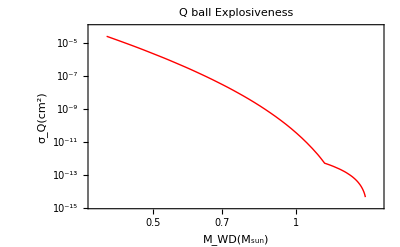

```mathematica
LogLogPlot[10^-4*(Interpolation[triggermass][M])^2,{M,0.4,1.4},FrameLabel->{"M_WD(M_sun)","σ_Q(cm^2)"},PlotLabel->"Q ball Explosiveness",Frame->True,PlotStyle->{Thick,Red},FrameStyle->Black]
```